A linha dos quadrados mínimos da diferença pode ser encontrada minimizando a soma 
d_1^2+d_2^2+...+d_n^2=∑_(i=1)^n d_1^2.
Estas são as diferenças.

Dada a equação da linha do modelo ŷ=b x+a, em que b é o slope e a o deslocamento vertical.
Os valores na linha do modelo são denotados ŷ.
Cada distância vertical é a diferença entre ŷ e y.

Substituindo ŷ em 
d_i=OverHat[y_i]-y_i 
por b x+a, temos 
d_i=b x_i+a-y_i.
Com isto, a soma da minimização dos quadrados da diferença fica
(b x_1+a-y_1)^2+(b x_2+a-y_2)^2+...+(b x_n+a-y_n)^2=∑_(i=1)^n (b x_i+a-y_i)^2.

Todos os x_i e y_i na função são conhecidos (são os dados).
O que fica para definir são b e a.
b e a são comuns a todos os termos; é necessário achar um valor único que torne a soma o menor número possível.

O problema é, para cada ponto a função tem um termo.
Por exemplo, para D={{4,5},{2,7},{9,1},{12,6},{5,3}},
(4 b+a-5)^2+(2 b+a-7)^2+(9 b+a-1)^2+(12 b+a-6)^2+(5 b+a-3)^2=

```mathematica
{Expand[(4 b+a-5)^2],Expand[(2b+a-7)^2],Expand[(9b+a-1)^2],Expand[(12b+a-6)^2],Expand[(5b+a-3)^2]}
```

{25-10 a+a^2-40 b+8 a b+16 b^2,49-14 a+a^2-28 b+4 a b+4 b^2,1-2 a+a^2-18 b+18 a b+81 b^2,36-12 a+a^2-144 b+24 a b+144 b^2,9-6 a+a^2-30 b+10 a b+25 b^2}

Somando os termos...

```mathematica
Expand[(4 b+a-5)^2]+Expand[(2b+a-7)^2]+Expand[(9b+a-1)^2]+Expand[(12b+a-6)^2]+Expand[(5b+a-3)^2]
```

120-44 a+5 a^2-260 b+64 a b+270 b^2

Agora temos termos a, b, a^2, b^2 e a b (e um termo livre).
Para cada um destes termos, temos um coeficiente.

```mathematica
FullSimplify[120-44 a+5 a^2-260 b+64a b+270 b^2]
```

120+a (-44+5 a)-260 b+64 a b+270 b^2

Não dá para agrupar só em a e b porque temos um termo a b.
Se não tivéssemos este termo,

```mathematica
FullSimplify[120-44 a+5 a^2-260 b+270 b^2]
```

120+a (-44+5 a)+10 b (-26+27 b)

Mesmo assim temos as potências.
Mas a função geral para minimizar para a e b é 120-44 a+5 a^2-260 b+64 a b+270 b^2.

Se não fosse a diferença ao quadrado, apenas simples,

```mathematica
4 b+a-5+2b+a-7+9b+a-1+12b+a-6+5b+a-3
```

-22+5 a+32 b

Ou seja, é o quadrado da diferença que introduz essa “multiplicidade de variáveis”.
Podemos começar com a simples, -22+5 a+32 b, para minimizar.

```mathematica
Plot3D[32b+5a-22,{a,-10,10},{b,-10,10},AxesLabel->Automatic]
```

-Graphics3D-

As derivadas parciais.
Mantendo b constante, (∂y)/(∂a)=5 (pois se b é uma constante, 32 b é derivado como 0);
mantendo a constante, (∂y)/(∂b)=32 (pois se a é uma constante, 5 a é derivado como 0).

```mathematica
{D[(32b+5a-22), a],D[(32b+5a-22), b]}
```

{5,32}

Então as diferenças simples têm parciais constantes.

Mas os extremos são igualar a zero.
Mas não dá para igualar estas derivadas a zero; elas são os próprios extremos.

Pausando para uma função qualquer arbitrária.

```mathematica
D[(0.1 x^3-2 x^2+10.3x-8.1), x]
```

10.3-4 x+0.3 x^2

```mathematica
Module[{f,df},Manipulate[f=a x^3+b x^2+c x+d;df=D[f, x];Plot[{f,df},{x,0,15}(*,PlotRange->{{0,15},{-10,20}}*)],{{a,0.1},0,0.2,0.001},{{b,-2},-2.2,-1.8,.01},{{c,10.3},5.3,15.3,.1},{{d,-8.1},-28.1,12.1,.1},Dynamic["Zeros: "<>ToString[Solve[df==0,x]]]]]
```

Mas estes não são extremos, são pontos de inflexão...
Nestas raízes, y é...

```mathematica
Clear[f1,f1ext]
f1=Function[x,0.1 x^3-2 x^2+10.3x-8.1];
f1ext=Solve[D[f1[x], x]==0,x]
```

{{x→3.48687},{x→9.84646}}

```mathematica
{f1[x/.First[f1ext]],f1[x/.Last[f1ext]]}
```

{7.73766,-5.12285}

Sem usar os dados, as derivadas parciais da soma da minimização dos quadrados da diferença ∂_a ∑_(i=1)^n (b x_i+a-y_i)^2 e ∂_b ∑_(i=1)^n (b x_i+a-y_i)^2 seriam

```mathematica
∑_(i=1)^n (b Subscript[x, i]+a-Subscript[y, i])
```

∑_(i=1)^n (a+b x_i-y_i)

```mathematica
{∂_a ∑_(i=1)^n (b Subscript[x, i]+a-Subscript[y, i])^2,∂_b ∑_(i=1)^n (b Subscript[x, i]+a-Subscript[y, i])^2}
```

{∑_(i=1)^n (2 a+2 b x_i-2 y_i),∑_(i=1)^n (2 a x_i+2 b x_i^2-2 x_i y_i)}

Sem os quadrados...

```mathematica
{∂_a ∑_(i=1)^n b Subscript[x, i]+a-Subscript[y, i],∂_b ∑_(i=1)^n b Subscript[x, i]+a-Subscript[y, i]}
```

{a-y_i,a-y_i+∑_(i=1)^n x_i}

Igualar a zero...

```mathematica
Solve[∑_(i=1)^n (2 a+2 b Subscript[x, i]-2 Subscript[y, i])==0,b]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[∑_(i=1)^n (2 a+2 b x_i-2 y_i)==0,b]

Usando os dados D na diferença sem quadrados, as diferenças simples têm parciais constantes. Nestas derivadas (números), y é

```mathematica
Clear[f2,f2ext]
f2=Function[{a,b},32b+5a-22];
f2ext=<|"a"->D[f2[a,b], a],"b"->D[f2[a,b], b]|>
```

<|a→5,b→32|>

A função é bidimensional e tem os extremos para cada variável/dimensão. Logo devemos plugar estes extremos na função bidimensional?

```mathematica
f2[f2ext["a"],f2ext["b"]]
```

1027

```mathematica
Dt[f2[a,b]]
```

5 Dt[a]+32 Dt[b]

```mathematica
Plot3D[32b+5a-22,{a,0,10},{b,22,42},AxesLabel->Automatic(*,Epilog->Line[{5,32}]*)]
```

-Graphics3D-

Acho que é por isso que a diferença é ao quadrado... Função linear não tem extremo.

Visualizar a diferença ao quadrado.

```mathematica
Clear[f3]
f3=Function[{a,b},120-44 a+5 a^2-260 b+64 a b+270 b^2];
Plot3D[f3[a,b],{a,-1000,1000},{b,-1000,1000}]
```

-Graphics3D-

```mathematica
{D[f3[a,b], a],D[f3[a,b], b]}
```

{-44+10 a+64 b,-260+64 a+540 b}

```mathematica
{Solve[D[f3[a,b], a]==0,a],Solve[D[f3[a,b], b]==0,b]}
```

{{{a→-2/5 (-11+16 b)}},{{b→1/135 (65-16 a)}}}

Invertido? (Não sei o significado.)

```mathematica
{Solve[D[f3[a,b], a]==0,b],Solve[D[f3[a,b], b]==0,a]}
```

{{{b→1/32 (22-5 a)}},{{a→-5/16 (-13+27 b)}}}

As derivadas parciais das bidimensionais ainda são bidimensionais, mas como achar seus extremos (números)? Parece que é encontrar a solução comum das equações parciais... Exatamente o que monta a matriz.

```mathematica
Solve[(D[f3[a,b], a]==0)&&(D[f3[a,b], b]==0),a]
```

{}

```mathematica
Solve[(-44+10 a+64 b==0)&&(-260+64 a+540 b==0),a]
```

{}

```mathematica
Solve[(D[f3[a,b], b]==0)&&(D[f3[a,b], a]==0),b]
```

{}

```mathematica
Solve[(-44+10 a+64 b==0)&&(-260+64 a+540 b==0),b]
```

{}

Talvez não tenha solução por causa destes dados.

O 2 antes das derivadas parciais é por causa da diferenciação do quadrado1. E o x_1 multiplicado extra na b?

```mathematica
{D[(b Subscript[x, 1]+a-Subscript[y, 1])^2, b],D[(b Subscript[x, 1]+a-Subscript[y, 1])^2, a]}
```

{2 x_1 (a+b x_1-y_1),2 (a+b x_1-y_1)}

Partial derivative for b of (b*x+a-y)^2

WolframAlphaQueryResults

É a chain rule.

A somatória de uma soma pode ser a soma das somatórias.2

∂_a ∑_(i=1)^n (b x_i+a-y_i)^2=
∑_(i=1)^n (2 a+2 b x_i-2 y_i)=
2n a+2∑_(i=1)^n b x_i-2 ∑_(i=1)^n y_i=
2 a n+2 b∑_(i=1)^n x_i-2 ∑_(i=1)^n y_i
e 
∂_b ∑_(i=1)^n (b x_i+a-y_i)^2=
∑_(i=1)^n (2 a x_i+2 b x_i^2-2 x_i y_i)=
2∑_(i=1)^n a x_i+2∑_(i=1)^n b x_i^2-2 ∑_(i=1)^n y_i x_i=
2a ∑_(i=1)^n x_i+2 b ∑_(i=1)^n x_i^2-2 ∑_(i=1)^n y_i x_i.

Em ∂_a , por algum motivo, ∑_(i=1)^n a vira n a.

Mas este não é o principal; mesmo na forma básica, as parciais já contam com uma separação das variáveis.

Igualando a zero,

2 a n+2 b ∑_(i=1)^n x_i-2 ∑_(i=1)^n y_i=0⇒
2a n+2b ∑_(i=1)^n x_i=2 ∑_(i=1)^n y_i
e
2a ∑_(i=1)^n x_i+2b ∑_(i=1)^n x_i^2-2 ∑_(i=1)^n y_i x_i=0⇒
2a ∑_(i=1)^n x_i+2b ∑_(i=1)^n x_i^2=2 ∑_(i=1)^n y_i x_i.

Dividindo ambos por 2,

a n+b ∑_(i=1)^n x_i=∑_(i=1)^n y_i e 
a ∑_(i=1)^n x_i+b ∑_(i=1)^n x_i^2=∑_(i=1)^n y_i x_i.

Este sistema é na forma 
a n+b r=s e 
a r+b t=u, onde 
r=∑_(i=1)^n x_i, 
s=∑_(i=1)^n y_i, 
t=∑_(i=1)^n x_i^2, 
u=∑_(i=1)^n y_i x_i.

Somando,
a n+b r+a r+b t=s+u

Para isolar b, 
b (r+t)=s+u-a (n- r)⇒
b=(s+u-a (n-r))/(r+t)
e a,
a (r+t)=s+u-b(r+t)⇒
a=(s+u-b(r+t))/(r+t).

Para resolver o sistema, antes de somar,

r(a n+b r)=r s e 
-n(a r+b t)=-n u, 
a r n+b r^2-a n r-b n t=r s-n u⇒
b(r^2 -n t)=rs-nu⇒
b=(r s-n u)/(r^2-n t).

Reescrevendo a primeira equação por a,

a n+b r=s⇒
a n=s-b r⇒
a=(s-b r)/n.

O paper pára aqui (sem substituir (r s-n u)/(r^2-n t) como b).

As equações normais são as equações das variáveis em função de x_i e y_i-(ŷ)_i, ou seja, a diferença entre o modelo e os dados.
(As variáveis compõem os coeficientes do modelo.)
Estas equações são o mínimo de cada variável em função da função diferença dados/modelo.
(Ou seja, igualar a derivada parcial de cada variável a zero.)
A função da diferença dados/modelo “como um todo” só tem mínimo se todas as variáveis ou derivadas parciais têm mínimo simultaneamente. Por isso o mínimo de cada variável é inputado em um sistema que deve ter resolução simultânea para todas as variáveis.
A função da diferença dados/modelo é a soma ou somatória de n instâncias da função diferença dado/modelo com x_i e y_i substituídos na função, vindos dos dados, e (ŷ)_i substituído na função vindo do modelo, com n a quantidade de pontos nos dados.
(Ou seja, a soma de todas as funções diferença modelo/dado determina os coeficientes desta função, que são os valores que compõem o sistema para solução.)
Na prática, como as variáveis são as incógnitas, são as somas dos x e y-ŷ dos dados e modelo que definem os coeficientes do sistema.
Ao resolver o sistema, temos os valores do mínimo de cada variável para a função modelo + diferença dados/modelo, o que são os coeficientes que compõem o modelo que minimiza estes números.

### Prática

O seguinte dado com fit cosseno manual em β e γ resulta nos seguintes coeficientes:
β=0.4
γ=0.7
τ=35.4
M=-0.6.
Com erro ao quadrado 39.0437.

```mathematica
(*isso deve sempre ser verdadeiro*)
Clear[M,τ,β,γ]
```

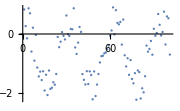

```mathematica
(*Modeling.nb points2b2*)
Clear[points1,vpar1]
points1={0.8284486071053614,0.2673766376785629,-0.14587103848031902,0.8659704680415028,0.6991054112068219,-0.5932855354991372,0.21297025528936597,-0.9010456996596811,-0.030879521202742576,-1.133049654303759,-1.4324089094905839,-1.270981884735523,-1.5552221204894652,-1.2586636022472573,-1.9093207045062175,-1.3759040972960583,-2.061605396624213,-1.2335920873943944,-1.8533437975699254,-1.8164746665727174,-1.6290120220853845,-1.7116595290663346,-1.352066224957822,-0.10037040026559799,-0.44472491816671944,-0.2596568963669798,0.06285429782538576,-0.06346957807609765,-0.18448352933728485,0.6246534612077154,-0.006174881643827068,-0.06502142909589814,0.1686536257918504,0.15891776406895763,0.8678106239728732,-0.4548811745532705,-0.6736415238084847,-0.2911906832115924,0.23732408561395746,0.07177387879911197,-1.3539139236619375,-1.5471260950874175,-1.7035617918354244,-1.2558811707264064,-1.6906494482483745,-1.2619354904647726,-1.3842843570445247,-2.2052825010307653,-1.265733123287958,-2.0947960534072982,-1.7080835495234936,-1.3518507792640269,-0.9615974393807152,-0.7494942516664271,-0.7338543826276729,-0.6534623436224303,-0.6252389174950516,-0.5204834884289617,-0.3874763587258824,-0.05758135540471643,0.11854240431761054,0.8981654306370527,-0.013977664048510086,0.8052506466173435,0.37661987319616574,0.32510264122148536,0.40646110744073427,-0.35807936440906396,0.4871767884679086,-0.7186521152394503,-1.094967842104894,-0.81830838248517,-1.3801571828450752,-0.8795611822154916,-1.517133287613289,-1.664771480472902,-1.3232941021894993,-2.219577478346638,-1.232400984641124,-1.2868048228555837,-2.178556885853927,-1.8343907689357255,-1.9693290041028009,-1.4278958877767378,-0.39267562356780833,-0.5961410991868128,-0.503018191117886,-0.23521525543185887,-0.69870089922561,0.176379284974584,-0.059940129728581315,0.0354238512007059,0.674986957155442,0.310189265494055,-0.04773396744340963,0.06766761693848689,0.7541576591238246,-0.35473834105713187,0.5942506338070388,0.5299567287605065,-0.6952077109359691};
ListPlot[points1,ImageSize->Small]
vpar1=<|"β"->0.4,"γ"->0.7,"τ"->35.4,"M"->-0.6|>;
```

A função do modelo é 
Ŷ(t)=M+A cos((2π t)/τ+ϕ), com a identidade trigonométrica, 
Ŷ(t)=M+A cos(ϕ) cos((2π t)/τ)-A sin(ϕ) sin((2π t)/τ), com os parâmetros, 
Ŷ(t)=M+β cos((2π t)/τ)-γ sin((2π t)/τ).

Tomando em alguns pontos

```mathematica
Clear[testt1,fmodelparam1]
testt1={11,30,50,65};
(*fmodelparam1 dá o modelo em um ponto*)
(*t na função modelo é baseado em 0, e não 1*)
fmodelparam1=Function[{t,M,τ,β,γ},M+β Cos[(2 π t)/τ]-γ Sin[(2 π t)/τ]]
```

Function[{t,M,τ,β,γ},M+β Cos[(2 π t)/τ]-γ Sin[(2 π t)/τ]]

```mathematica
Table[fmodelparam1[t,vpar1["M"],vpar1["τ"],vpar1["β"],vpar1["γ"]],{t,testt1}]
```

{-1.39861,0.202727,-1.30698,0.206027}

```mathematica
fmodelparam1[10,vpar1["M"],vpar1["τ"],β,γ]
```

-0.6-0.2027 β-0.979241 γ

Simulando dados nestes pontos

```mathematica
Clear[testdata1]
testdata1={{11,-1},{30,0.5},{50,-1.4},{65,0.1}};
```

A função diferença dados/modelo é 
ΔY(t)=∑_(i=1)^n y_i-[M+β cos((2π t_i)/τ)-γ sin((2π t_i)/τ)]

```mathematica
Clear[fmodeldif1part1,fmodeldif1part2,fmodeldif1indiv,fmodeldifsq1indiv,
fmodeldif1,fmodeldifsq1]
(*testando a somatória*)
fmodeldif1part1=Function[{t,data},∑_(i=1)^Length[data] data[[i]][[2]]];
fmodeldif1part2=Function[{t,data},
∑_(i=1)^Length[data] fmodelparam1[t[[i]],vpar1["M"],vpar1["τ"],β,γ]];
(*teste de diferença em um ponto*)
(*fmodeldif1indiv dá a diferença entre um dado e o modelo em um ponto*)
fmodeldif1indiv=Function[{M,τ,β,γ,t,y},y-fmodelparam1[t,M,τ,β,γ]];
fmodeldifsq1indiv=Function[{M,τ,β,γ,t,y},(y-fmodelparam1[t,M,τ,β,γ])^2];
(*a(s) função(ões)*)
(*estas funções, sem os parâmetros definidos, dão as funções a minimizar 
(igualar as parciais a zero) -- ainda separadas por termo -- usar 
Simplify[] --, e com os parâmetros, as somas dos resíduos.*)
(*t é uma lista de posições (x também chamado t), com início em 0, que 
também deve constar em data, que são pontos (x,y)*)
fmodeldif1=Function[{M,τ,β,γ,t,data},
∑_(i=1)^Length[data] (data[[i]][[2]]-fmodelparam1[t[[i]],M,τ,β,γ])];
fmodeldifsq1=Function[{M,τ,β,γ,t,data},
∑_(i=1)^Length[data] (data[[i]][[2]]-fmodelparam1[t[[i]],M,τ,β,γ])^2];
```

Testes da somatória...

```mathematica
{fmodeldif1part1[testt1,testdata1],fmodeldif1part2[testt1,testdata1]}
```

{-1.8,-2.4-0.134741 β+0.224373 γ}

Testando as diferenças para os pontos...
São tantas diferenças quanto pontos.
Aqui estou passando índice baseado em 1 para testt1 (ao invés de baseado 0) porque ele não é um ts, é uma lista contendo as posições. (?)

```mathematica
Print[Column[Table[fmodeldif1indiv[vpar1["M"],vpar1["τ"],β,γ,testt1[[i+1]],testdata1[[i+1]][[2]]],{i,0,Length[testt1]-1}]]]
```

-0.4+0.372411 β+0.928068 γ
1.1-0.574787 β-0.818303 γ
-0.8+0.852408 β+0.522877 γ
0.7-0.515292 β-0.857015 γ

Soma das diferenças...

```mathematica
-0.4+0.372411 β+0.928068 γ+1.1-0.574787 β-0.818303 γ+-0.8+0.852408 β+0.522877 γ+0.7-0.515292 β-0.857015 γ
```

0.6+0.13474 β-0.224373 γ

Soma das diferenças via somatória.

```mathematica
Clear[residual1]
residual1=fmodeldif1[vpar1["M"],vpar1["τ"],β,γ,testt1,testdata1];
Simplify[residual1]
```

0.6+0.134741 β-0.224373 γ

Bateu. Minimizar em β e γ.

```mathematica
{D[residual1, β],D[residual1, γ]}
```

{0.134741,-0.224373}

Estou tendo as derivadas constantes porque estou fazendo erro linear e não quadrático...

```mathematica
Clear[residualsq1];
residualsq1=fmodeldifsq1[vpar1["M"],vpar1["τ"],β,γ,testt1,testdata1];
Print[residualsq1];
Simplify[residualsq1]
```

(0.7-0.515292 β-0.857015 γ)^2+(1.1-0.574787 β-0.818303 γ)^2+(-0.8+0.852408 β+0.522877 γ)^2+(-0.4+0.372411 β+0.928068 γ)^2

2.5+1.4612 β^2-4.57914 γ+2.5388 γ^2+β (-3.64772+3.40658 γ)

A somatória veio sem somar.

Minimizar em β e γ.

```mathematica
Print[Column[{D[residualsq1, β],"\n",D[residualsq1, γ]}]]
```

-1.03058 (0.7-0.515292 β-0.857015 γ)-1.14957 (1.1-0.574787 β-0.818303 γ)+1.70482 (-0.8+0.852408 β+0.522877 γ)+0.744823 (-0.4+0.372411 β+0.928068 γ)


-1.71403 (0.7-0.515292 β-0.857015 γ)-1.63661 (1.1-0.574787 β-0.818303 γ)+1.04575 (-0.8+0.852408 β+0.522877 γ)+1.85614 (-0.4+0.372411 β+0.928068 γ)

Vem sem somar, somando...

```mathematica
Clear[partials1]
partials1={Simplify[D[residualsq1, β]],Simplify[D[residualsq1, γ]]};
Print[Column[{partials1[[1]],"\n",partials1[[2]]}]]
```

-3.64772+2.92239 β+3.40658 γ


-4.57914+3.40658 β+5.07761 γ

Estas são as duas parciais, uma em cada variável.
As duas têm que ser igualadas a zero simultaneamente.

```mathematica
Clear[minpars1]
minpars1=Solve[partials1[[1]]==0&&partials1[[2]]==0]
```

{{β→0.903683,γ→0.295548}}

Estes parâmetros substituem o β e γ definidos visualmente, mas mantendo o M e τ.

O erro ao quadrado para os parâmetros definidos visualmente é

```mathematica
Clear[residual1v]
residual1v=fmodeldifsq1[vpar1["M"],vpar1["τ"],vpar1["β"],vpar1["γ"],testt1,testdata1];
residual1v
```

0.267158

```mathematica
Clear[difindivs1v]
difindivs1v=Table[fmodeldifsq1indiv[vpar1["M"],vpar1["τ"],vpar1["β"],vpar1["γ"],testt1[[i]],testdata1[[i]][[2]]],{i,Length[testt1]}]
```

{0.158892,0.0883713,0.00865326,0.0112417}

```mathematica
Total[difindivs1v]
```

0.267158

Batendo as diferenças manualmente...

```mathematica
{(-1+1.3986119758301152)^2,(0.5-0.20272690722148112)^2,(-1.4+1.3069770906904363)^2,(0.1-0.2060270811124157)^2}
```

{0.158892,0.0883713,0.00865326,0.0112417}

Estar diferente da diferença no modelo original (39.0437) é por causa dos dados.

As diferenças com os parâmetros minimizados...

```mathematica
difindivs1=Table[fmodeldifsq1indiv[vpar1["M"],vpar1["τ"],β,γ,testt1[[i]],testdata1[[i]][[2]]]/.First[minpars1],{i,Length[testt1]}]
```

{0.0444494,0.114736,0.0155855,0.000359067}

```mathematica
Total[difindivs1]
```

0.17513

Diminuiu!

```mathematica
Clear[residual1]
residual1=fmodeldifsq1[vpar1["M"],vpar1["τ"],β,γ,testt1,testdata1]/.First[minpars1];
residual1
```

0.17513

Agora, usando os dados.

Minimizar β e γ. Pegar a somatória do resíduo sem estas variáveis.

```mathematica
fmodelparam1
```

Function[{t,M,τ,β,γ},M+β Cos[(2 π t)/τ]-γ Sin[(2 π t)/τ]]

```mathematica
fmodelparam1[0,vpar1["M"],vpar1["τ"],vpar1["β"],vpar1["γ"]]
```

-0.2

```mathematica
fmodeldif1indiv
```

Function[{M,τ,β,γ,t,y},y-fmodelparam1[t,M,τ,β,γ]]

```mathematica
fmodeldif1
```

Function[{M,τ,β,γ,t,data},∑_(i=1)^Length[data] (data⟦i⟧⟦2⟧-fmodelparam1[t⟦i⟧,M,τ,β,γ])]

Nas chamadas ao fmodelparam1, passar t baseado em 0.
Como uso o ts para passar, montar o ts a partir de 0.

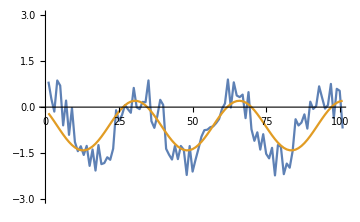

visual rss: 39.0437

min rss fun: 101. (1.12753+M^2+0.489868 β^2+M (1.25139-0.0848016 β-0.0520183 γ)+β (-0.405116-0.0398594 γ)-0.782083 γ+0.510132 γ^2)

min rss par: <|M→202. (0.625696+M-0.0424008 β-0.0260091 γ),β→-40.9167-8.56497 M+98.9532 β-4.0258 γ,γ→-78.9904-5.25385 M-4.0258 β+103.047 γ|>

min rss solution: {{M→-0.589475,β→0.393061,γ→0.751851}}

min rss: {38.8924}

min model fun: -0.589475+0.393061 Cos[0.177491 t]-0.751851 Sin[0.177491 t]

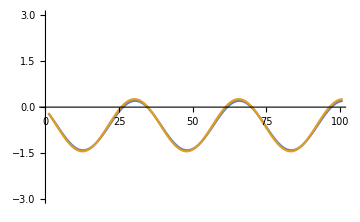

Â: {0.848397}

ϕ̂: {2.05251}

```mathematica
Module[{dta,dtapoints,mdl,mdlpoints,ts,difsq,rss,
minrssf,minrsspar,minrsssol,minrss,Ahat,K,ϕhat},
(*definir o dado, criar o ts, "discretizar" ou samplear o modelo*)
dta=points1;
(*Print[dta];*)
ts=Range[0,Length[dta]-1];(*já gerar o ts baseado no dta*)
(*gerar o dtapoints baseado no ts (base 0) e dta (base 1)*)
dtapoints=Table[{i,dta[[i+1]]},{i,ts}];
(*Print[dtapoints];*)
(*discretize*)
mdl=Table[fmodelparam1[t,vpar1["M"],vpar1["τ"],vpar1["β"],vpar1["γ"]],{t,0,Length[dta]-1}];(*checado*)
(*Print[mdl];*)
Print[ListLinePlot[{dta,mdl},ImageSize->Medium,PlotRange->{{0,Length[dta]-1},{-3,3}}]];
(*Print[{Length[dta],Length[dtapoints],Length[mdl],Length[ts]}];*)

(*calcular o resíduo visual*)
rss=fmodeldifsq1[vpar1["M"],vpar1["τ"],vpar1["β"],vpar1["γ"],ts,dtapoints];
Print["visual rss: ",rss];
(*testes de debug de rss*)
(*Print[fmodelparam1[ts[[1]],vpar1["M"],vpar1["τ"],vpar1["β"],vpar1["γ"]]];*)
(*Print["first data is ",First[dta]];
Print["first model is ",First[mdl]];
Print["first res should be ",ToString[0.828449+0.2]];
Print["first res is ",fmodeldif1indiv[vpar1["M"],vpar1["τ"],vpar1["β"],vpar1["γ"],First[ts],First[dta]]];
Print["first res sq^2 is ",fmodeldifsq1indiv[vpar1["M"],vpar1["τ"],vpar1["β"],vpar1["γ"],First[ts],First[dta]]];*)

(*calcular o resíduo mínimo*)
(*paper: τ não tem estimativa.*)
minrssf=fmodeldifsq1[M,vpar1["τ"],β,γ,ts,dtapoints];
Print["min rss fun: ",Simplify[minrssf]];
minrsspar=<|
"M"->Simplify[D[minrssf, M]],
"β"->Simplify[D[minrssf, β]],
"γ"->Simplify[D[minrssf, γ]]
|>;
Print["min rss par: ",minrsspar];
minrsssol=Solve[
minrsspar["M"]==0&&
minrsspar["β"]==0&&
minrsspar["γ"]==0
];
Print["min rss solution: ",minrsssol];
minrss=minrssf/.minrsssol;
Print["min rss: ",minrss];

(*plotar o minimizado*)
(*TODO: porquê necessário First? abaixo*)
minmdlf=First[fmodelparam1[t,M,vpar1["τ"],β,γ]/.minrsssol];
Print["min model fun: ",minmdlf];
(*Plot[minmdlf,{t,0,100}]*)
minmdl=Table[minmdlf,{t,0,Length[dta]-1}];
Print[ListLinePlot[{mdl,minmdl},ImageSize->Medium,PlotRange->{{0,Length[dta]-1},{-3,3}}]];

(*estimar amplitude e acrofase*)
Ahat=√(β^2+γ^2)/.minrsssol;
K=1;
ϕhat=ArcTan[-γ/β]+K π/.minrsssol;
Print["Â: ",Ahat];
Print["ϕ̂: ",ϕhat];
]
```

TODO: exibir (e resolver) a NE (equações normais) em forma matricial.
Valores M, τ, β, γ estão vazando para o global e contaminando as funções.

Testes de ts.
Aparentemente, mudar a razão de ts só vai escalonar o eixo x.
O problema é usar o valor de ts para acessar os índices dos dados.
Os dados têm de ser acessados pelos índices de ts, não por seus valores.
Mas neste caso, ts não vai servir para mais absolutamente nada.
Ou, criar os pontos (indexar) dos dados por ts.

```mathematica
fmodelparam1
```

Function[{t,M,τ,β,γ},M+β Cos[(2 π t)/τ]-γ Sin[(2 π t)/τ]]

101

{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,128,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,170,172,174,176,178,180,182,184,186,188,190,192,194,196,198,200}

{{0,0.828449},{1,0.267377},{2,-0.145871},{3,0.86597},{4,0.699105},{5,-0.593286},{6,0.21297},{7,-0.901046},{8,-0.0308795},{9,-1.13305},{10,-1.43241},{11,-1.27098},{12,-1.55522},{13,-1.25866},{14,-1.90932},{15,-1.3759},{16,-2.06161},{17,-1.23359},{18,-1.85334},{19,-1.81647},{20,-1.62901},{21,-1.71166},{22,-1.35207},{23,-0.10037},{24,-0.444725},{25,-0.259657},{26,0.0628543},{27,-0.0634696},{28,-0.184484},{29,0.624653},{30,-0.00617488},{31,-0.0650214},{32,0.168654},{33,0.158918},{34,0.867811},{35,-0.454881},{36,-0.673642},{37,-0.291191},{38,0.237324},{39,0.0717739},{40,-1.35391},{41,-1.54713},{42,-1.70356},{43,-1.25588},{44,-1.69065},{45,-1.26194},{46,-1.38428},{47,-2.20528},{48,-1.26573},{49,-2.0948},{50,-1.70808},{51,-1.35185},{52,-0.961597},{53,-0.749494},{54,-0.733854},{55,-0.653462},{56,-0.625239},{57,-0.520483},{58,-0.387476},{59,-0.0575814},{60,0.118542},{61,0.898165},{62,-0.0139777},{63,0.805251},{64,0.37662},{65,0.325103},{66,0.406461},{67,-0.358079},{68,0.487177},{69,-0.718652},{70,-1.09497},{71,-0.818308},{72,-1.38016},{73,-0.879561},{74,-1.51713},{75,-1.66477},{76,-1.32329},{77,-2.21958},{78,-1.2324},{79,-1.2868},{80,-2.17856},{81,-1.83439},{82,-1.96933},{83,-1.4279},{84,-0.392676},{85,-0.596141},{86,-0.503018},{87,-0.235215},{88,-0.698701},{89,0.176379},{90,-0.0599401},{91,0.0354239},{92,0.674987},{93,0.310189},{94,-0.047734},{95,0.0676676},{96,0.754158},{97,-0.354738},{98,0.594251},{99,0.529957},{100,-0.695208}}

{-0.2,-0.468241,-0.752911,-1.01851,-1.23193,-1.36655,-1.40558,-1.34416,-1.18995,-0.962178,-0.689241,-0.405176,-0.145404,0.0576812,0.178758,0.202727,0.126601,-0.040129,-0.276672,-0.553531,-0.836186,-1.08939,-1.28157,-1.38876,-1.3976,-1.30698,-1.1282,-0.883563,-0.603565,-0.323123,-0.0772054,0.103522,0.196524,0.190204,0.0853496,-0.104964,-0.357006,-0.639349,-0.916784,-1.15472,-1.32348,-1.40203,-1.38057,-1.26178,-1.06047,-0.801735,-0.517849,-0.244207,-0.0149298,0.141392,0.205266,0.168728,0.0363334,-0.175408,-0.440095,-0.72472,-0.993794,-1.21376,-1.3572,-1.40622,-1.3547,-1.20908,-0.987513,-0.717622,-0.433064,-0.169322,0.0407168,0.170862,0.204884,0.138542,-0.0198927,-0.250663,-0.524995,-0.808679,-1.06634,-1.26585,-1.38234,-1.40127,-1.32029,-1.14949,-0.91017,-0.632176,-0.35017,-0.0993171,0.0891037,0.191597,0.195382,0.0999877,-0.0826916,-0.329877,-0.610744,-0.890273,-1.13361,-1.3104,-1.39861,-1.38724,-1.27771,-1.08366,-0.829312,-0.546366,-0.270107}

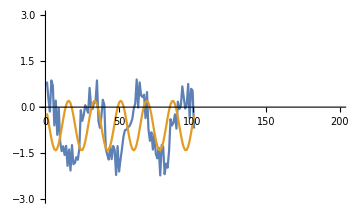

```mathematica
Module[{dta,ts,dtapoints},
dta=points1;
ts=Range[0,(Length[dta]-1)*2,2];
Print[Length[ts]];
Print[ts];
dtapoints=Table[{i-1,dta[[i]]},{i,Range[1,Length[ts]]}];
Print[dtapoints];
mdl=Table[fmodelparam1[t,vpar1["M"],vpar1["τ"],vpar1["β"],vpar1["γ"]],{t,ts}];
Print[mdl];
Print[ListLinePlot[{dta,mdl},ImageSize->Medium,PlotRange->{{0,200},{-3,3}}]];
];
```

O problema é que o plot como pontos (ListLinePlot) não escala o eixo x.
Só que se resolver por Plot[], como no ActStudio é plotado?
Parte do problema é que a largura do plot por pontos é definida pela lista de dados, e não por um scaling. Se estipularmos uma largura diferente para a discretização do modelo via scaling do ts, ele fica com largura diferente dos dados. Interpolar a lista de dados seria “feio”, mas talvez a única solução.

```mathematica
Module[{dta,ts,dtapoints},
dta=points1;
ts=Range[0,(Length[dta]-1)*2,2];
Print[Length[ts]];
Print[ts];
dtapoints=Table[{i-1,dta[[i]]},{i,Range[1,Length[ts]]}];
Print[dtapoints];
mdl=Table[fmodelparam1[t,vpar1["M"],vpar1["τ"],vpar1["β"],vpar1["γ"]],{t,ts}];
Print[mdl];
Print[Plot[{dta,mdl},ImageSize->Medium,{t,...}<PlotRange->{{0,200},{-3,3}}]];
];
```

1	https://www.youtube.com/watch?v=29cVVsokRms&t=237s&list=WL&index=3

2	ERIC - Least Squares Procedures